# Tight Focusing of LG beams with arbitrary polarisation states

## A brief introduction to the theory of tightly focused paraxial beams

The electric field E(ρ,φ,z) at the focal plane for an aplanatic lens with focal length f is given by the Richards and Wolf’s Diffraction Integral (RWDI) [10.1098/rspa.1959.0200]: 

E(ρ,φ,z)=-(ⅈ f)/λ ∫_0^α ∫_0^(2 π) Sinθ  A(θ,ϕ) exp[ ⅈ k ρ Sinθ Cos(φ-ϕ)]exp[ⅈ k z Cosθ] dθ dϕ, 

where  α = ArcSin(NA/n) is the maximum angular aperture of the objective, n is the refractive index of the medium of the medium where the focusing occurs, NA is the lens numerical aperture and A is the transformation of the input field U(r)=(U_x,U_y ,0) after the objective. Explicitly, A is given by 

A_x=√Cosθ {  [Cosθ+(1-Cosθ)Sin^2 ϕ]U_x+(Cosθ-1)Cosϕ Sinϕ U_y},
A_y=√Cosθ{  (Cosθ-1)Cosϕ Sinϕ U_x+[Cosθ+(1-Cosθ)Cos^2 ϕ]U_y},
A_z=-√Cosθ Sinθ { Cosϕ U_x+Sin ϕ U_y}.

It must be noticed that the 3D electric field at the focus satisfies Maxwell’s equations. Since closed solutions for RWDI are hard or even impossible to obtain, the components of the electric field under tight focusing in this notes are found by numerical integration. 

For the case of an arbitrary polarised Laguerre-Gauss beam, a simplified set of integrals can be obtained and you can find them in the PDF file.

## Instructions

I designed the notebook to evaluate the Definitions section automatically, so you directly can start to play with the calculations. Here, I present a small introduction to the functions. 

 - Efz0[xmax, dx, ℓ, NA, n]={EXx,EXy,EXz,EYx,EYy,EYz} :  Calculates the Cartesian contributions of  a focused LG with topological charge ℓ due to a lens with numerical aperture NA occurring in a linear and homogeneous medium with refractive index n. The calculation is performed in a numerical window within the intervals -x_max≤ x ≤ x_max and -y_max≤ y ≤ y_max.
 
  - Eprop[xmax, dx, zmin, zmax, dz, ℓ, NA, n]={EXx,EXy,EXz,EYx,EYy,EYz} :  Calculates the Cartesian contributions of a focused LG for different planes z_min≤ z ≤ z_max with topological charge ℓ due to a lens with numerical aperture NA occurring in a linear and homogeneous medium with refractive index n . The calculation is performed in a numerical window within the intervals -x_max≤ x ≤ x_max and -y_max≤ y ≤ y_max with resolution of dx.
  
  - Ep[α, β ]={Ex,Ey,Ez} :  Given the array of the Cartesian contributions of the field it constructs the focused field given the parameters of the incident field. The incident beam is constructed E_in = ( Cos α x̂+ ⅇ^(i β) Sin α  ŷ )U(r).
  
   - Int[ψ ]  Plots the intensity profile of the complex scalar amplitude ψ.

   - Ph[ψ ]  Plots the phase profile of the complex scalar amplitude ψ.

### Example 1 : LG00

```mathematica
AbsoluteTiming[E00=Efz0[1.5,0.07,0,0.95,1]][[1]]
```

39.222

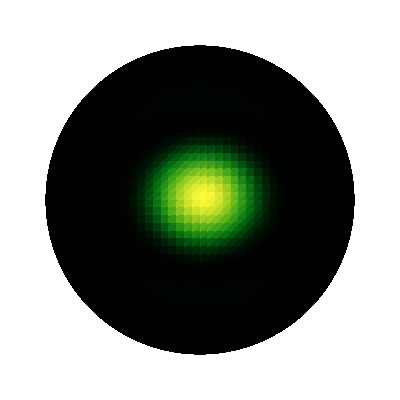
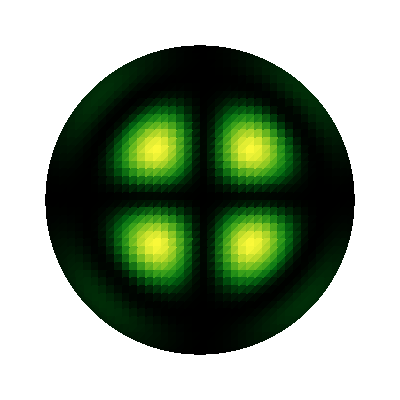
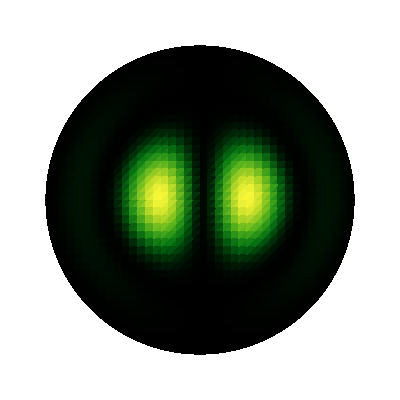

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Linearly polarised in x*)
Map[Int,Ep[E00,0,0]]
Map[Ph,Ep[E00,0,0]]
```

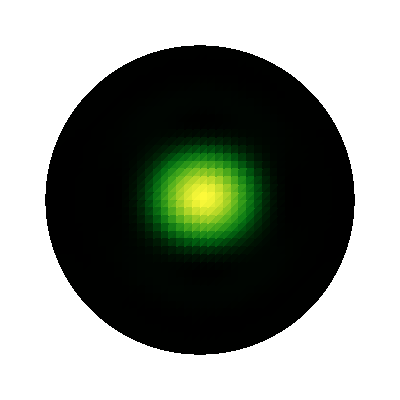
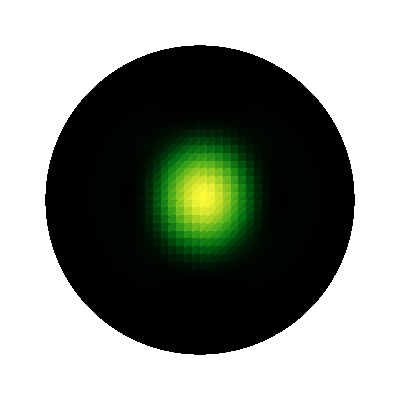
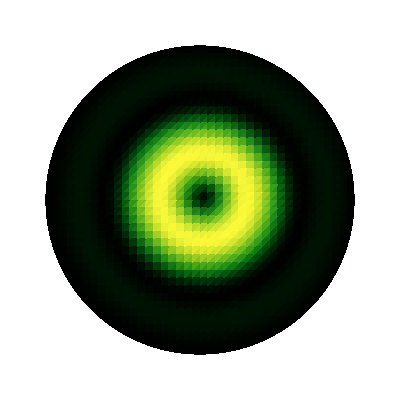

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Circular polarization in *)
Map[Int,Ep[E00,π/4,-π/2]]
Map[Ph,Ep[E00,π/4,-π/2]]
```

### Example 2 : LG01

```mathematica
AbsoluteTiming[E01=Efz0[1.5,0.07,1,0.95,1]][[1]]
```

29.8555

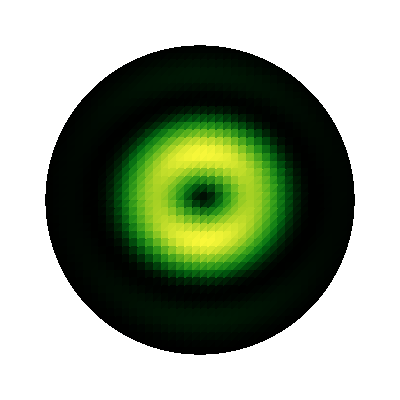
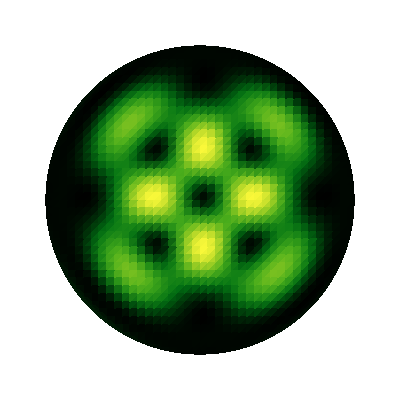
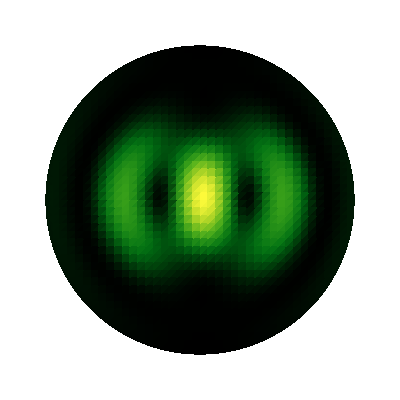

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Linearly polarised in x*)
Map[Int,Ep[E01,0,0]]
Map[Ph,Ep[E01,0,0]]
```

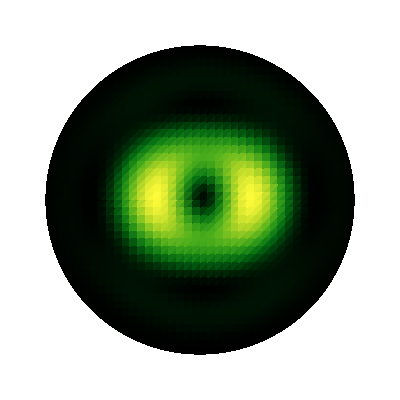
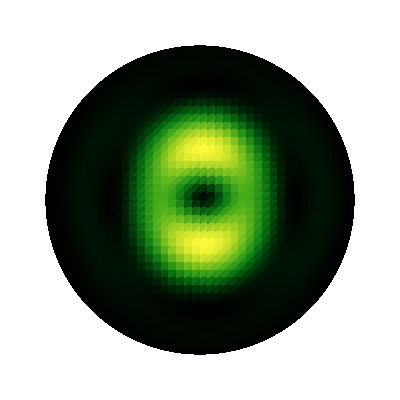
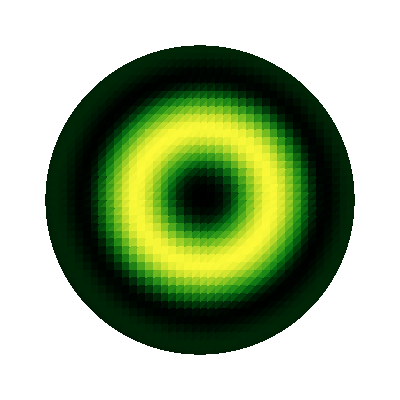

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Circular polarization in *)
Map[Int,Ep[E01,π/4,+π/2]]
Map[Ph,Ep[E01,π/4,+π/2]]
```

### Example 3 : Vector beams

```mathematica
AbsoluteTiming[E01=Efz0[1.5,0.07,1,0.95,1]][[1]]
```

40.7425

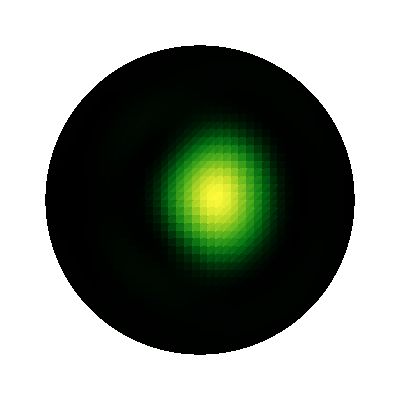
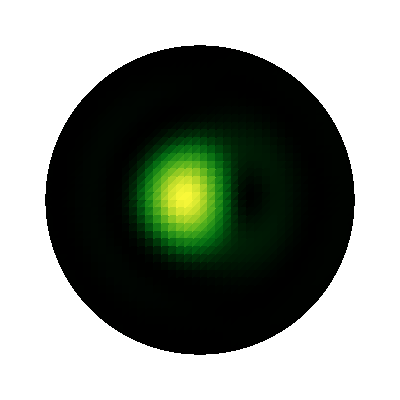
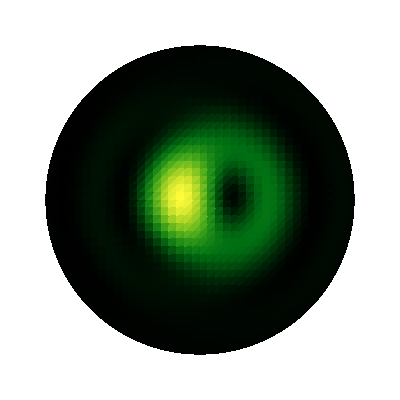

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Lemon Topology*)
Map[Int,Ep[E00,π/4,π/2]+Ep[E01,π/4,-π/2]]
Map[Ph,Ep[E00,π/4,π/2]+Ep[E01,π/4,-π/2]]
```

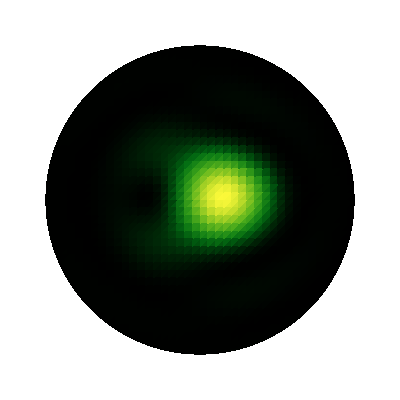
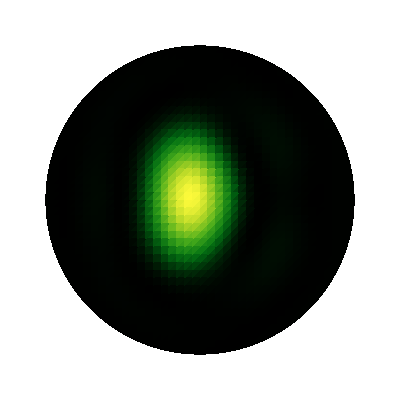
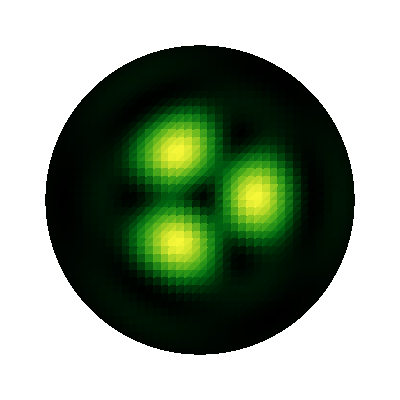

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Star Topology*)
Map[Int,Ep[E00,π/4,-π/2]+Ep[E01,π/4,π/2]]
Map[Ph,Ep[E00,π/4,-π/2]+Ep[E01,π/4,π/2]]
```

## Definitions

```mathematica
Ph[ψ_]:=ListDensityPlot[Arg[ψ],ColorFunction->(Hue[Rescale[#,{0,2π},{0,1}]]&),PlotRange->All,ColorFunctionScaling->False,Frame->None,BoundaryStyle->Directive[Transparent,Thick],DataRange->{{-1.5,1.5},{-1.5,1.5}},RegionFunction->Function[{x,y,f},(x)^2+(y)^2<2]];
Int[ψ_]:=ListDensityPlot[Abs[ψ]^2,ColorFunction->ColorData["AvocadoColors"],PlotRange->All,Frame->None,BoundaryStyle->Directive[Transparent,Thick],DataRange->{{-1.5,1.5},{-1.5,1.5}},RegionFunction->Function[{x,y,f},(x)^2+(y)^2<2]];
k=2π;
lg[ρ_,ℓ_]:=ρ^Abs[ℓ] ⅇ^(-ρ^2);
```

#### Field produced by the X-polarised component a LG beam

```mathematica
(* Resulting X-component of the polarization due to a initially X-polarised LG0l mode *)LGxx[ρ_,φ_,z_,ℓ_,a_,b_]:=ⅇ^(ⅈ ℓ φ)NIntegrate[√Cos[θ] Sin[θ] lg[(Sin[θ]/Sin[α]),ℓ](1/2(1+Cos[θ]) BesselJ[ℓ,k ρ Sin[θ]]+1/4(1-Cos[θ])( BesselJ[ℓ+2,k ρ Sin[θ]] ⅇ^(ⅈ 2φ)+BesselJ[ℓ-2,k ρ Sin[θ]] ⅇ^(-ⅈ 2φ)))*Exp[I k z Cos[θ]],{θ,a,b}];(* Resulting Y-component of the polarization due to a initially X-polarised LG0l mode *)LGxy[ρ_,φ_,z_,ℓ_,a_,b_]:= ⅇ^(ⅈ ℓ φ)(-1/(2ⅈ))NIntegrate[√Cos[θ] Sin[θ] lg[(Sin[θ]/Sin[α]),ℓ]((Cos[θ]-1)(BesselJ[ℓ+2,k ρ Sin[θ]] ⅇ^(2ⅈ φ)-BesselJ[ℓ-2,k ρ Sin[θ]] ⅇ^(-2ⅈ φ)))*Exp[I k z Cos[θ]],{θ,a,b}];
(* Resulting Z-component of the polarization due to a initially X-polarised LG0l mode *)LGxz[ρ_,φ_,z_,ℓ_,a_,b_]:=ⅇ^(ⅈ ℓ φ)(-ⅈ/2)NIntegrate[√Cos[θ] Sin[θ]^2 lg[(Sin[θ]/Sin[α]),ℓ](BesselJ[ℓ+1,k ρ Sin[θ]] ⅇ^(ⅈ φ)-BesselJ[ℓ-1,k ρ Sin[θ]] ⅇ^(-ⅈ φ))*Exp[I k z Cos[θ]],{θ,a,b}];
```

#### Field produced by the Y-polarised component a LG beam

```mathematica
(* Resulting X-component of the polarization due to a initially Y-polarised LG0l mode *)LGyx[ρ_,φ_,z_,ℓ_,a_,b_]:=ⅇ^(ⅈ ℓ φ)(-1/(2ⅈ))NIntegrate[√Cos[θ] Sin[θ] lg[(Sin[θ]/Sin[α]),ℓ]((Cos[θ]-1)(BesselJ[ℓ+2,k ρ Sin[θ]] ⅇ^(2ⅈ φ)-BesselJ[ℓ-2,k ρ Sin[θ]] ⅇ^(-2ⅈ φ)))*Exp[I k z Cos[θ]],{θ,a,b}];
(* Resulting X-component of the polarization due to a initially Y-polarised LG0l mode *)
LGyy[ρ_,φ_,z_,ℓ_,a_,b_]:= 
ⅇ^(ⅈ ℓ φ)NIntegrate[√Cos[θ] Sin[θ] lg[(Sin[θ]/Sin[α]),ℓ](1/2(1+Cos[θ]) BesselJ[ℓ,k ρ Sin[θ]]-1/4(1-Cos[θ])( BesselJ[ℓ+2,k ρ Sin[θ]] ⅇ^(ⅈ 2φ)+BesselJ[ℓ-2,k ρ Sin[θ]] ⅇ^(-ⅈ 2φ)))*Exp[I k z Cos[θ]],{θ,a,b}];
(* Resulting X-component of the polarization due to a initially Y-polarised LG0l mode *)LGyz[ρ_,φ_,z_,ℓ_,a_,b_]:=ⅇ^(ⅈ ℓ φ)(-1/2)NIntegrate[√Cos[θ] Sin[θ]^2 lg[(Sin[θ]/Sin[α]),ℓ](BesselJ[ℓ+1,k ρ Sin[θ]] ⅇ^(ⅈ φ)+BesselJ[ℓ-1,k ρ Sin[θ]] ⅇ^(-ⅈ φ))*Exp[I k z Cos[θ]],{θ,a,b}];
```

#### Construction of the beams

```mathematica
Efz0[xmax_,dx_,ℓ_,NA_,n_]:=Block[{EXx,EXy,EXz,EYx,EYy,EYz,α=ArcSin[NA/n]},
EXx=ParallelTable[LGxx[√(x^2+y^2),ArcTan[x,y],0,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx}];
EXy=ParallelTable[LGxy[√(x^2+y^2),ArcTan[x,y],0,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx}];
EXz=ParallelTable[LGxz[√(x^2+y^2),ArcTan[x,y],0,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx}];
EYx=ParallelTable[LGyx[√(x^2+y^2),ArcTan[x,y],0,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx}];
EYy=ParallelTable[LGyy[√(x^2+y^2),ArcTan[x,y],0,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx}];
EYz=ParallelTable[LGyz[√(x^2+y^2),ArcTan[x,y],0,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx}];
Return[{EXx,EXy,EXz,EYx,EYy,EYz}]
];
```

```mathematica
Efprop[xmax_,dx_,zmin_,zmax_,dz_,ℓ_,NA_,n_]:=Block[{EXx,EXy,EXz,EYx,EYy,EYz,α=ArcSin[NA/n]},
EXx=ParallelTable[LGxx[√(x^2+y^2),ArcTan[x,y],z,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx},{z,zmin,zmax,dz}];
EXy=ParallelTable[LGxy[√(x^2+y^2),ArcTan[x,y],z,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx},{z,zmin,zmax,dz}];
EXz=ParallelTable[LGxz[√(x^2+y^2),ArcTan[x,y],z,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx},{z,zmin,zmax,dz}];
EYx=ParallelTable[LGyx[√(x^2+y^2),ArcTan[x,y],z,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx},{z,zmin,zmax,dz}];
EYy=ParallelTable[LGyy[√(x^2+y^2),ArcTan[x,y],z,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx},{z,zmin,zmax,dz}];
EYz=ParallelTable[LGyz[√(x^2+y^2),ArcTan[x,y],z,ℓ,0,α],{y,-xmax,xmax,dx},{x,-xmax,xmax,dx},{z,zmin,zmax,dz}];
Return[{EXx,EXy,EXz,EYx,EYy,EYz}]
];
```

```mathematica
(*Constructing the arbitrary polarised*)
Ep[E_,α_,β_]:={Cos[α]*E[[1]]+Sin[α]Exp[I β]*E[[4]],Cos[α]*E[[2]]+Sin[α]Exp[I β]*E[[5]],Cos[α]*E[[3]]+Sin[α]Exp[I β]*E[[6]]};
```